```mathematica
Directory[]
```

/home/goluckyryan

```mathematica
Ogata=Drop[Import["P_outfile_25F_Ogata.dat"],{1}];
Dirac=Drop[Import["P_outfile_25F_Dirac.dat"],{1}];
OgataS=Drop[Import["PS_outfile_25F_Ogata.dat"],{1}];
DiracS=Drop[Import["PS_outfile_25F_Dirac.dat"],{1}];
```

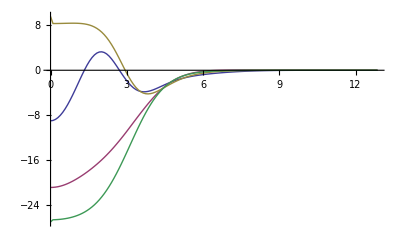

```mathematica
ListPlot[{
Ogata[[1;;-1,{1,4}]],
Ogata[[1;;-1,{1,5}]],
Dirac[[1;;-1,{1,4}]],
Dirac[[1;;-1,{1,5}]]
},
Joined->True,PlotRange->All]
```

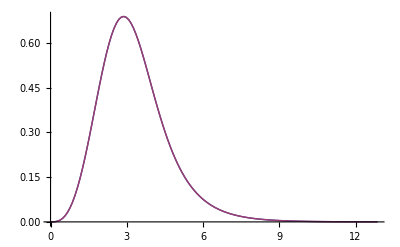

```mathematica
ListPlot[{
Ogata[[1;;-1,{1,3}]],
Dirac[[1;;-1,{1,3}]]
},
Joined->True,PlotRange->All]
```

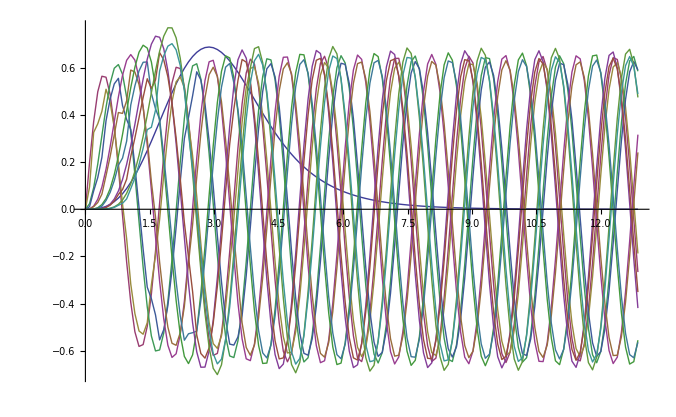

```mathematica
ListPlot[{
Ogata[[1;;-1,{1,3}]],
Ogata[[1;;-1,{1,9}]],
(*Ogata[[1;;-1,{1,10}]],*)
Dirac[[1;;-1,{1,9}]],
(*Dirac[[1;;-1,{1,10}]]*)
Ogata[[1;;-1,{1,11}]],
(*Ogata[[1;;-1,{1,12}]],*)
Dirac[[1;;-1,{1,11}]],
(*Dirac[[1;;-1,{1,12}]]*)
Ogata[[1;;-1,{1,13}]],
(*Ogata[[1;;-1,{1,14}]],*)
Dirac[[1;;-1,{1,13}]],
(*Dirac[[1;;-1,{1,14}]]*)
Ogata[[1;;-1,{1,15}]],
Dirac[[1;;-1,{1,15}]],
Ogata[[1;;-1,{1,17}]],
Dirac[[1;;-1,{1,17}]],
Ogata[[1;;-1,{1,19}]],
Dirac[[1;;-1,{1,19}]]
},
Joined->True,PlotRange->All]
```

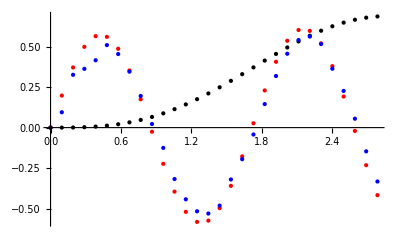

```mathematica
ListPlot[{
Ogata[[1;;30,{1,3}]],
Ogata[[1;;30,{1,9}]],
Dirac[[1;;30,{1,9}]]
},
Joined->False,PlotRange->All, PlotStyle->{Black, Red, Blue}]
```

```mathematica
Dirac[[1;;10,{1,9}]]
```

{{0.,0.},{0.096,0.094866},{0.192,0.326177},{0.288,0.362848},{0.384,0.415806},{0.48,0.509453},{0.576,0.45427},{0.672,0.345444},{0.768,0.195365},{0.864,0.022053}}

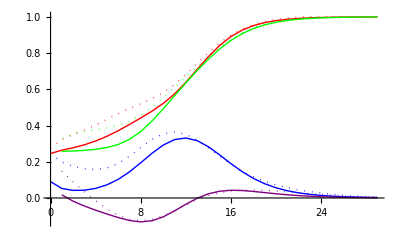

```mathematica
ListPlot[{
OgataS[[1;;30,{1,3}]],
OgataS[[2;;30,{1,10}]],
OgataS[[1;;30,{1,4}]],
OgataS[[2;;30,{1,11}]],
DiracS[[1;;30,{1,3}]],
DiracS[[2;;30,{1,10}]],
DiracS[[1;;30,{1,4}]],
DiracS[[2;;30,{1,11}]]
},Joined->True, PlotStyle->{Directive[Red, Dotted],Directive[Green, Dotted],Directive[Blue, Dotted],Directive[Purple, Dotted],Red, Green, Blue, Purple}]
```

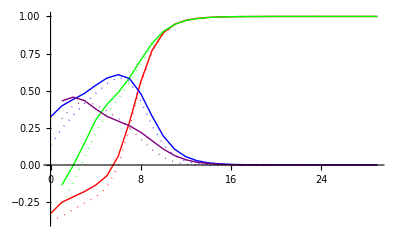

```mathematica
ListPlot[{
OgataS[[1;;30,{1,5}]],
OgataS[[2;;30,{1,12}]],
OgataS[[1;;30,{1,6}]],
OgataS[[2;;30,{1,13}]],
DiracS[[1;;30,{1,5}]],
DiracS[[2;;30,{1,12}]],
DiracS[[1;;30,{1,6}]],
DiracS[[2;;30,{1,13}]]
},Joined->True, PlotStyle->{Directive[Red, Dotted],Directive[Green, Dotted],Directive[Blue, Dotted],Directive[Purple, Dotted],Red, Green, Blue, Purple}]
```

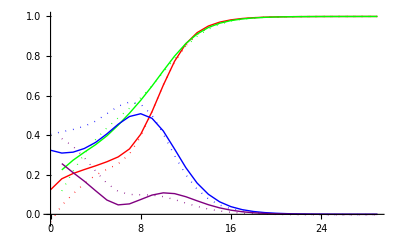

```mathematica
ListPlot[{
OgataS[[1;;30,{1,7}]],
OgataS[[2;;30,{1,14}]],
OgataS[[1;;30,{1,8}]],
OgataS[[2;;30,{1,15}]],
DiracS[[1;;30,{1,7}]],
DiracS[[2;;30,{1,14}]],
DiracS[[1;;30,{1,8}]],
DiracS[[2;;30,{1,15}]]
},Joined->True, PlotStyle->{Directive[Red, Dotted],Directive[Green, Dotted],Directive[Blue, Dotted],Directive[Purple, Dotted],Red, Green, Blue, Purple}]
```